```mathematica
myAbs[x_]:=Piecewise[{{x,x>=0},{-x,x<0}}]

dphi = b T0 Erf[x]
dphi1=RealAbs[b T0 Erf[x]]-b T0 / 2
dphi2 = RealAbs[dphi1] - b T0 / 4
dphi3 = RealAbs[dphi2] - b T0 / 8

phi=Integrate[dphi, {x,0,y}]
phi1=Integrate[dphi1,{x,0,y}, Assumptions -> {b>0,T0>0} ]//FullSimplify
phi2=PiecewiseExpand[Integrate[dphi2, {x,0,y}, Assumptions -> {b>0,T0>0}],Assumptions -> {b>0,T0>0}]//FullSimplify
phi3=Integrate[dphi3, {x,0,y}, Assumptions -> {b>0,T0>0}]//FullSimplify
PiecewiseExpand[Integrate[RealAbs[x],x],Assumptions->{x∈Reals}]//FullSimplify
```

b T0 Erf[x]

-(b T0)/2+RealAbs[b T0 Erf[x]]

-(b T0)/4+RealAbs[-(b T0)/2+RealAbs[b T0 Erf[x]]]

-(b T0)/8+RealAbs[-(b T0)/4+RealAbs[-(b T0)/2+RealAbs[b T0 Erf[x]]]]

(b T0 (-1+ⅇ^(-y^2)+√π y Erf[y]))/(√π)

Integrate[-(b T0)/2+RealAbs[b T0 Erf[x]],{x,0,y},Assumptions→b>0&&T0>0]

Integrate[-(b T0)/4+RealAbs[-(b T0)/2+b T0 RealAbs[Erf[x]]],{x,0,y},Assumptions→b>0&&T0>0]

Integrate[-(b T0)/8+RealAbs[-(b T0)/4+RealAbs[-(b T0)/2+RealAbs[b T0 Erf[x]]]],{x,0,y},Assumptions→b>0&&T0>0]

Piecewise[{{-x^2/2, x<0}, {x^2/2, True}}]

```mathematica
phi=Integrate[dphi, x]
phi1=Integrate[dphi1,x, Assumptions -> x∈Reals ]//FullSimplify
phi2=Integrate[dphi2, x]//FullSimplify
phi3=Integrate[dphi3, x]//FullSimplify
Integrate[myAbs[x],x]
```

b T0 ((ⅇ^(-x^2))/(√π)+x Erf[x])

Piecewise[{{1/2 b T0 ((2 ⅇ^(-x^2))/(√π)+x-2 x Erfc[x]), b T0 Erf[x]≥0}, {1/2 b T0 (-(2 ⅇ^(-x^2))/(√π)-3 x+2 x Erfc[x]), True}}]

Piecewise[{{1/4 b T0 ((4 ⅇ^(-x^2))/(√π)+x-4 x Erfc[x]), b T0 Erf[x]≥0&&2 b T0 Erf[x]≥b T0}, {1/4 b T0 (-(4 ⅇ^(-x^2))/(√π)-7 x+4 x Erfc[x]), b T0 Erf[x]<0&&b T0 (1+2 Erf[x])≤0}, {1/4 b T0 (-(4 ⅇ^(-x^2))/(√π)+x-4 x Erf[x]), b T0 Erf[x]≥0&&2 b T0 Erf[x]<b T0}, {1/4 b T0 ((4 ⅇ^(-x^2))/(√π)+x+4 x Erf[x]), True}}]

Piecewise[{{1/8 b T0 ((8 ⅇ^(-x^2))/(√π)+x-8 x Erfc[x]), b T0 Erf[x]≥0&&2 b T0 Erf[x]≥b T0&&b T0≥4 b T0 Erfc[x]}, {1/8 b T0 (-(8 ⅇ^(-x^2))/(√π)-7 x-8 x Erf[x]), b T0 Erf[x]<0&&b T0 (3+4 Erf[x])≤0}, {1/8 b T0 (-(8 ⅇ^(-x^2))/(√π)+x-8 x Erf[x]), b T0 Erf[x]≥0&&2 b T0 Erf[x]<b T0&&4 b T0 Erf[x]≤b T0}, {1/8 b T0 ((8 ⅇ^(-x^2))/(√π)+x+8 x Erf[x]), b T0 Erf[x]<0&&b T0 (1+4 Erf[x])≥0}, {1/8 b T0 (-(8 ⅇ^(-x^2))/(√π)+5 x-8 x Erf[x]), 1/2≤Erf[x]<3/4&&b T0>0}, {(b ⅇ^(-x^2) T0)/(√π)+(5 b T0 x)/8+b T0 x Erf[x], b T0 (1+2 Erf[x])≤0&&b T0 (3+4 Erf[x])>0}, {(b ⅇ^(-x^2) T0)/(√π)-(3 b T0 x)/8+b T0 x Erf[x], 2 b T0 Erf[x]<b T0&&4 b T0 Erf[x]>b T0}, {1/8 b T0 (-(8 ⅇ^(-x^2))/(√π)-3 x-8 x Erf[x]), b T0 (1+4 Erf[x])<0&&b T0 (1+2 Erf[x])>0}, {-1/8 b T0 x, True}}]

Piecewise[{{-x^2/2, x≤0}, {x^2/2, True}}]

```mathematica
pieceToAbs[expr_]:=expr/. Piecewise[{{a_,cond1_},{b_,cond2_}}]:>(1/2) ((a+b)+(a-b) Sign[x])

phi1//FullSimplify
pieceToAbs[phi1]//FullSimplify
```

Piecewise[{{1/2 b T0 ((2 ⅇ^(-x^2))/(√π)+x-2 x Erfc[x]), b T0 Erf[x]≥0}, {1/2 b T0 (-(2 ⅇ^(-x^2))/(√π)-3 x+2 x Erfc[x]), True}}]

Piecewise[{{1/2 b T0 ((2 ⅇ^(-x^2))/(√π)+x-2 x Erfc[x]), b T0 Erf[x]≥0}, {1/2 b T0 (-(2 ⅇ^(-x^2))/(√π)-3 x+2 x Erfc[x]), True}}]

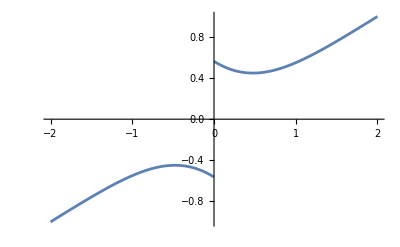

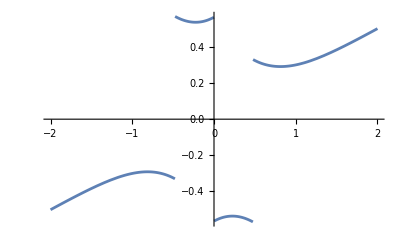

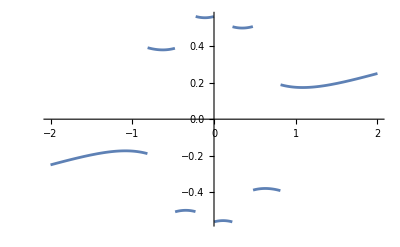

```mathematica
phii1[y_]:=phi1/.{x->y,T0->1,b->1}
phii2[y_]:=phi2/.{x->y,T0->1,b->1}
phii3[y_]:=phi3/.{x->y,T0->1,b->1}
Show[Plot[phii1[y],{y,-2,2}]]
Show[Plot[phii2[y],{y,-2,2}]]
Show[Plot[phii3[y],{y,-2,2}]]
```